```mathematica
SetDirectory["/Users/rafaelcordoba/Documents/MATLAB"]
```

/Users/rafaelcordoba/Documents/MATLAB

## Define partial waves h^I_ℓ

#### Define coefficeints asnd functions

```mathematica
Nn=3; 
Subscript[δ, l_,i_]:=0;
t[s_,μ_]:=-1/2 (s-4) *(1-μ);
u[s_,μ_]:=-1/2 (s-4) *(1+μ);
Subscript[A, l_,n_][i_,s_,phi_]:=0;
Subscript[A, l_,n_,m_][i_,s_,phi_]:=0;
Subscript[B, l_,n_][i_,s_,phi_]:=0;
Subscript[B, l_,n_,m_][i_,s_,phi_]:=0;
Subscript[A, l_][i_]:=0;
Subscript[Aa, l_,n_][i_,s_]:=0;
Subscript[Aa, l_,n_,m_][i_,s_]:=0;
Subscript[Bb, l_,n_][i_,s_]:=0;
Subscript[Bb, l_,n_,m_][i_,s_]:=0;

zet[s_]:=SetPrecision[(2-Sqrt[4-s])/(2+Sqrt[4-s]),100];
_n_[s_]:=zet[s]^n;
_n_[phi_]:=E^(I*n* phi);
_(n_,l_)[s_]:=Chop[NIntegrate[LegendreP[l,μ]* _n[t[s,μ]],{μ,-1,1},AccuracyGoal ->60,WorkingPrecision->100]];_(n_,m_,l_)[s_]:=Chop[NIntegrate[LegendreP[l,μ]*_m[u[s,μ]]* _n[t[s,μ]],{μ,-1,1},AccuracyGoal ->60,WorkingPrecision->100]];


Subscript[δ, l_,i_]:=1/;l==i;

Subscript[A, l_][i_]:=2 *(Nn+2) *Subscript[δ, l,0]/;i==0;Subscript[A, l_][i_]:=0/;i==1;Subscript[A, l_][i_]:=4* Subscript[δ, l,0]/;i==2;

Subscript[A, l_,n_][i_,s_,phi_]:=2* Nn *Subscript[δ, l,0] * _n[phi]+2* _(n,l)[s]/;i==0;Subscript[A, l_,n_][i_,s_,phi_]:=2*_(n,l)[s]/;i==1;Subscript[A, l_,n_][i_,s_,phi_]:=2 *_(n,l)[s]/;i==2;

Subscript[Aa, l_,n_][i_,s_]:=2* Nn* Subscript[δ, l,0]  _n[s]+2 _(n,l)[s]/;i==0;Subscript[Aa, l_,n_][i_,s_]:=2 _(n,l)[s]/;i==1;Subscript[Aa, l_,n_][i_,s_]:=2 _(n,l)[s]/;i==2;

Subscript[B, l_,n_][i_,s_,phi_]:=4* Subscript[δ, l,0]*  _n[phi]+2 *(Nn+1)* _(n,l)[s]/;i==0;Subscript[B, l_,n_][i_,s_,phi_]:=-2* _(n,l)[s]/;i==1;Subscript[B, l_,n_][i_,s_,phi_]:=4 *Subscript[δ, l,0] * _n[phi]+2* _(n,l)[s]/;i==2;

Subscript[Bb, l_,n_][i_,s_]:=4 Subscript[δ, l,0]  _n[s]+2 (Nn+1) _(n,l)[s]/;i==0;Subscript[Bb, l_,n_][i_,s_]:=-2 _(n,l)[s]/;i==1;Subscript[Bb, l_,n_][i_,s_]:=4 Subscript[δ, l,0]  _n[s]+2 _(n,l)[s]/;i==2;


Subscript[A, l_,n_,m_][i_,s_,phi_]:=2* Nn *_n[phi] *_(m,l)[s]+2 * _m[phi] *_(n,l)[s]+2 *_(n,m,l)[s]/;i==0;Subscript[A, l_,n_,m_][i_,s_,phi_]:=2* _m[phi]* _(n,l)[s]+2*_(n,m,l)[s]/;i==1;Subscript[A, l_,n_,m_][i_,s_,phi_]:=2*_m[phi]*  _(n,l)[s]+2* _(n,m,l)[s]/;i==2;

Subscript[Aa, l_,n_,m_][i_,s_]:=2 *Nn* _n[s] *_(m,l)[s]+2 * _m[s] *_(n,l)[s]+2* _(n,m,l)[s]/;i==0;Subscript[Aa, l_,n_,m_][i_,s_]:=2* _m[s] *_(n,l)[s]+2*_(n,m,l)[s]/;i==1;Subscript[Aa, l_,n_,m_][i_,s_]:=2*_m[s] * _(n,l)[s]+2* _(n,m,l)[s]/;i==2;


Subscript[B, l_,n_,m_][i_,s_,phi_]:= _n[phi] _(m,l)[s]+ _m[phi] _(n,l)[s]+Nn* _(n,m,l)[s]/;i==0;
Subscript[B, l_,n_,m_][i_,s_,phi_]:=- _n[phi] _(m,l)[s]- _m[phi] _(n,l)[s]/;i==1;
Subscript[B, l_,n_,m_][i_,s_,phi_]:= _n[phi] _(m,l)[s]+ _m[phi] _(n,l)[s]/;i==2;

Subscript[Bb, l_,n_,m_][i_,s_]:= _n[s] _(m,l)[s]+ _m[s] _(n,l)[s]+Nn *_(n,m,l)[s]/;i==0;Subscript[Bb, l_,n_,m_][i_,s_]:=- _n[s] _(m,l)[s]- _m[s] _(n,l)[s]/;i==1;Subscript[Bb, l_,n_,m_][i_,s_]:= _n[s] _(m,l)[s]+ _m[s] _(n,l)[s]/;i==2;

h[l_, i_, s_,phi_, nmax_, mmax_] :=

N[Sqrt[(s-4)/s]*(Pi/4 )*(Subscript[f, 0]*Subscript[A, l][i]+Sum[Subscript[ρ, 1][n,m]*Subscript[A, l,n,m][i,s,phi]+Subscript[B, l,n,m][i,s,phi] *Subscript[ρ, 2][n,m],{n,1,nmax},{m,1,mmax}]+Sum[Subscript[σ, 1][n] *Subscript[A, l,n][i,s,phi]+Subscript[σ, 2][n] *Subscript[B, l,n][i,s,phi],{n,1,nmax}]),100];

hunphy[l_, i_, s_, nmax_, mmax_] :=N[Sqrt[(s-4)/s]*(Pi/4 )*(Subscript[f, 0]*Subscript[A, l][i]+Sum[Subscript[ρ, 1][n,m]*Subscript[Aa, l,n,m][i,s]+Subscript[Bb, l,n,m][i,s] *Subscript[ρ, 2][n,m],{n,1,nmax},{m,1,mmax}]+Sum[Subscript[σ, 1][n] *Subscript[Aa, l,n][i,s]+Subscript[σ, 2][n] *Subscript[Bb, l,n][i,s],{n,1,nmax}]),100];



f[l_, i_, s_, nmax_, mmax_] :=N[(1/4 )*(Subscript[f, 0]*Subscript[A, l][i]+Sum[Subscript[ρ, 1][n,m]*Subscript[Aa, l,n,m][i,s]+Subscript[Bb, l,n,m][i,s] *Subscript[ρ, 2][n,m],{n,1,nmax},{m,1,mmax}]+Sum[Subscript[σ, 1][n] *Subscript[Aa, l,n][i,s]+Subscript[σ, 2][n] *Subscript[Bb, l,n][i,s],{n,1,nmax}]),100];
Hextend[l_,i_,s_,phi_,nmax_,mmax_,k_]:=N[Sqrt[(s-4)/s]*(Pi/4 )*(Sum[Subscript[ρ, 1][n,m]*Subscript[A, l,n,m][i,s,phi]+Subscript[B, l,n,m][i,s,phi] *Subscript[ρ, 2][n,m],{n,nmax+1,nmax+k},{m,nmax+1,nmax+k}]+Sum[Subscript[ρ, 1][n,m]*Subscript[A, l,n,m][i,s,phi]+Subscript[B, l,n,m][i,s,phi] *Subscript[ρ, 2][n,m],{n,1,nmax},{m,nmax+1,mmax+k}]+Sum[Subscript[ρ, 1][n,m]*Subscript[A, l,n,m][i,s,phi]+Subscript[B, l,n,m][i,s,phi] *Subscript[ρ, 2][n,m],{n,nmax+1,nmax+k},{m,1,mmax}]+Sum[Subscript[σ, 1][n] *Subscript[A, l,n][i,s,phi]+Subscript[σ, 2][n] *Subscript[B, l,n][i,s,phi],{n,nmax+1,nmax+k}]),100];


Fextend[l_,i_,s_,nmax_,mmax_,k_]:=N[(1/4 )*(Sum[Subscript[ρ, 1][n,m]*Subscript[Aa, l,n,m][i,s]+Subscript[Bb, l,n,m][i,s] *Subscript[ρ, 2][n,m],{n,nmax+1,nmax+k},{m,nmax+1,nmax+k}]+Sum[Subscript[ρ, 1][n,m]*Subscript[Aa, l,n,m][i,s]+Subscript[Bb, l,n,m][i,s] *Subscript[ρ, 2][n,m],{n,1,nmax},{m,nmax+1,mmax+k}]+Sum[Subscript[ρ, 1][n,m]*Subscript[Aa, l,n,m][i,s]+Subscript[Bb, l,n,m][i,s] *Subscript[ρ, 2][n,m],{n,nmax+1,nmax+k},{m,1,mmax}]+Sum[Subscript[σ, 1][n] *Subscript[Aa, l,n][i,s]+Subscript[σ, 2][n] *Subscript[Bb, l,n][i,s],{n,nmax+1,nmax+k}]),100];

selectl[l_,i_]:=l;
selectl[l_,i_]:=2l/; Mod[i,2]== 0;
selectl[l_,i_]:=2l+1/; Mod[i,2]== 1;

nu0=0;
z[nu_]:=(Sqrt[4-nu0]-Sqrt[4-nu])/(Sqrt[4-nu0]+Sqrt[4-nu]);
nuz[zdisk_]=(16zdisk+nu0-2zdisk nu0+zdisk^2 nu0)/(1+zdisk)^2;
nuphi[phi_]=nu0+(8-2nu0)/(1+Cos[phi]);
dnuphi[phi_]=D[nuphi[phi],phi];
phii[x_,n_]:=Sin[n x];


nmax=7;
mmax=7;
ell=4; 
Table[{selectl[l,k],k,l},{k,0,2},{l,0,ell}]
SetDirectory["/Users/rafaelcordoba/Documents/MATLAB/Experiments"]
MeV=1/140;
mpi=140*MeV;
GeV=1000*MeV;
```

{{{0,0,0},{2,0,1},{4,0,2},{6,0,3},{8,0,4}},{{1,1,0},{3,1,1},{5,1,2},{7,1,3},{9,1,4}},{{0,2,0},{2,2,1},{4,2,2},{6,2,3},{8,2,4}}}

/Users/rafaelcordoba/Documents/MATLAB/Experiments

#### Example h^0_0(5), nmax=2:

Create M evaluation points s_i:

```mathematica
M=64;
vphi=Table[N[(i-1/2)Pi/M,12],{i,1,M}];
vnu=N[nuphi[vphi],30];
ds=N[dnuphi[vphi],30];
nmax=4;
mmax=4;
vars=Variables[N[(Subscript[f, 0]+Sum[Subscript[ρ, 1][n,m]+Subscript[ρ, 2][n,m],{n,1,nmax},{m,1,mmax}]+Sum[Subscript[σ, 1][n] +Subscript[σ, 2][n] ,{n,1,nmax}]),100]];

Chop[Coefficient[h[0,1,vnu[[1]],vphi[[1]],3,3],vars]+Coefficient[Hextend[0,1,vnu[[1]],vphi[[1]],3,3,1],vars]-Coefficient[h[0,1,vnu[[1]],vphi[[1]],4,4],vars]]

Chop[Coefficient[f[0,1,3,3,3]+Fextend[0,1,3,3,3,1],vars]-Coefficient[f[0,1,3,4,4],vars]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
CloseKernels[]; LaunchKernels[19];$KernelCount
```

16

# Generate a bunch whole of data with circle mapping

```mathematica
Do[
M=iM^2;
mmax=nmax;
ell=15; 
nu0=0;
vnu0=3;
p=100;
 
(*generate nu and phi evaluation*)
vphi=Table[N[(i-1/2)Pi/M,30],{i,1,M}];
vnu=N[nuphi[vphi],100];
ds=N[dnuphi[vphi],100];
(*generate variables for functionals evaluation*)
vars=Variables[N[(Subscript[f, 0]+Sum[Subscript[ρ, 1][n,m]+Subscript[ρ, 2][n,m],{n,1,nmax},{m,1,mmax}]+Sum[Subscript[σ, 1][n] +Subscript[σ, 2][n] ,{n,1,nmax}]),100]];
 
(*generate H coefficeints *)
polys=Table[h[selectl[l,k],k,vnu[[n]],vphi[[n]],nmax,nmax],{k,0,2},{l,0,ell},{n,1,Length[vnu]}];
H=Table[Coefficient[polys[[k+1,l+1,n]],vars],{k,0,2},{l,0,ell},{n,1,Length[vnu]}];
(*generate F coefficeints at s=3*)
polys2=Table[f[selectl[l,i],i,vnu0,nmax,nmax],{i,0,2},{l,0,ell}];
F=Table[Coefficient[polys2[[k+1,l+1]],vars],{k,0,2},{l,0,ell}];
(*generate Funphysical s=0-4 coefficeints *)
vnuunphy=Table[i,{i,0.2,4,0.2}];
wavenumbers={{0,0},{2,0},{1,1}}; (*first is isospin, then angular momentum*)
polys3=Table[f[wavenumbers[[j,2]],wavenumbers[[j,1]],vnuunphy[[i]],nmax,nmax],{i,1,Length[vnuunphy]},{j,1,Length[wavenumbers]}];
Fun04=Table[Coefficient[polys3[[i,j]],vars],{i,1,Length[vnuunphy]},{j,1,Length[wavenumbers]}];
(*generate Fun for CSB s=1/2,1,3/2,2 coefficeints *)
vnuunphy=Table[i/2,{i,1,4}];
polys4=Table[f[wavenumbers[[j,2]],wavenumbers[[j,1]],vnuunphy[[i]],nmax,nmax],{i,1,Length[vnuunphy]},{j,1,Length[wavenumbers]}];
Fun=Table[Coefficient[polys4[[i,j]],vars],{i,1,Length[vnuunphy]},{j,1,Length[wavenumbers]}];
(*find values to compare up to 2GeV *)
poscut12GeV=Position[vnu,_?(#>(2*GeV)^2&)][[1,1]];
vnuphy=vnu[[Range[1,poscut12GeV]]];
vphiphy=vphi[[Range[1,poscut12GeV]]];
(*extract H coefficeints with the above requirement *)
polys5phy={polys[[1,1,Range[1,poscut12GeV]]],polys[[3,1,Range[1,poscut12GeV]]],polys[[2,1,Range[1,poscut12GeV]]],polys[[1,2,Range[1,poscut12GeV]]]};
polys5phyF={Table[N[(Sqrt[(vnuphy[[jj]]-4)/vnuphy[[jj]]]*Pi)^(-1),100]*polys[[1,1,jj]],{jj,1,poscut12GeV}],Table[N[(Sqrt[(vnuphy[[jj]]-4)/vnuphy[[jj]]]*Pi)^(-1),100]*polys[[3,1,jj]],{jj,1,poscut12GeV}],Table[N[(Sqrt[(vnuphy[[jj]]-4)/vnuphy[[jj]]]*Pi)^(-1),100]*polys[[2,1,jj]],{jj,1,poscut12GeV}],Table[N[(Sqrt[(vnuphy[[jj]]-4)/vnuphy[[jj]]]*Pi)^(-1),100]*polys[[1,2,jj]],{jj,1,poscut12GeV}]};
Hexp=Table[Table[Coefficient[polys5phy[[i,j]],vars],{j,1,Dimensions[polys5phy][[2]]}],{i,1,Dimensions[polys5phy][[1]]}];
Fexp=Table[Table[Coefficient[polys5phyF[[i,j]],vars],{j,1,Dimensions[polys5phy][[2]]}],{i,1,Dimensions[polys5phy][[1]]}];
xexp=vnuphy;
(*generate K_ij kernel coefficeints *)

vK0=Table[Subscript[v, i],{i,2M}];
vK0[[1]]=0;
Do[vK0[[i]]=(1-(-1)^(i-1))/(2M)Cot[((i-1)π)/(2M)],{i,2,2M}];
K=Table[Subscript[k, i,j],{i,1,M},{j,1,M}];
Do[K[[i,j]]=N[N[vK0[[Mod[i+j-(2M+1),4M]+1]],p]-vK0[[Mod[i-j,4M]+1]],p],{i,1,M},{j,1,M}];

(*store coefficeints *)
Export["Fvecyifei"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",F];
Export["Hexp"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",Hexp];
Export["Fexp"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",Fexp];
Export["Xexp"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",xexp];
Export["Fun0-4"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",Fun04];
Export["Funvecyifei"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",Fun];
Export["hmatyifei"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",H];
Export["Kernel"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",K];
Export["vnuvals"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",vnu];
Export["dsvals"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",ds];

,{iM,9,9,2},{nmax,45,50,5}]
```

```mathematica
NN=3;
Do[
M=iM^2;L=20;ell=15;
ν0=0;
p=100; (*precision for the following computations*)
Clear[z];
z[ν_]=(√(4-ν0)-√(4-ν))/(√(4-ν0)+√(4-ν));xϕ[ϕ_]=ν0+(8-2 ν0)/(1+Cos[ϕ]);
dxϕ[ϕ_]=D[xϕ[ϕ],ϕ];Δϕ=π/M;
vϕ=Table[N[(i-1/2)Δϕ,p],{i,1,M}];vx=xϕ[vϕ];vdxϕ=dxϕ[vϕ];

Mπ=140;
s0=(2000/Mπ)^2;n0=Length[Select[vx,#≤s0&]]; 

FFS0factor=√(1/(2π)^4 3/(16π)√((vx-4)/vx));FFP1factor=√(1/(2π)^4 1/(24π)(vx-4)^(3/2)/(√vx));FFD0factor=1/(4 π^3)√((3π)/15)1/vx^(1/4)((vx-4)/4)^(5/4);


FF3factor=Join[{FFS0factor},{FFP1factor},{FFD0factor}];



ints0[n_,nl_]:=((Δϕ vx^n vdxϕ)/vx[[n0]]^(n+nl))[[1;;n0]];
vintS00=ints0[0,2];vintS01=ints0[1,2];vintS02=ints0[2,2];
vintP1m1=ints0[-1,2];vintP10=ints0[0,2];vintP11=ints0[1,2];
vintD0m2=ints0[-2,3];vintD0m1=ints0[-1,3];vintD00=ints0[0,3];
αs2GeV=0.3145887440;mu2GeV=3.6/Mπ;md2GeV=6.5/Mπ;
SVZP1[n_]=1/(2π)^4(1/(4π(n+2))(1+αs2GeV/π));SVZS0[n_]=(mu2GeV^2+md2GeV^2)/(2π)^4(3/(4π(n+2))(1+13/3 αs2GeV/π));SVZD0[n_]=1/(2π)^4(1/(4π(n+3))(11/10-17/18 αs2GeV/π));
SVZSR={SVZS0[0],SVZS0[1],SVZS0[2],SVZP1[-1],SVZP1[0],SVZP1[1],SVZD0[-2],SVZD0[-1],SVZD0[0]};




Export["GTB/intS00at2M="<>ToString[M]<>".mat",vintS00];Export["GTB/intS01at2M="<>ToString[M]<>".mat",vintS01];Export["GTB/intS02at2M="<>ToString[M]<>".mat",vintS02];
Export["GTB/intP1m1at2M="<>ToString[M]<>".mat",vintP1m1];Export["GTB/intP10at2M="<>ToString[M]<>".mat",vintP10];Export["GTB/intP11at2M="<>ToString[M]<>".mat",vintP11];
Export["GTB/intD0m2at2M="<>ToString[M]<>".mat",vintD0m2];Export["GTB/intD0m1at2M="<>ToString[M]<>".mat",vintD0m1];Export["GTB/intD00at2M="<>ToString[M]<>".mat",vintD00];
Export["GTB/SVZSRat2M="<>ToString[M]<>".mat",SVZSR];
Export["GTB/FF3factorM="<>ToString[M]<>".mat",FF3factor];
,{iM,9,9,2},{nmax,2,29,3}]
```

```mathematica
SVZSR
```

{3.0935×10^-7,2.06233×10^-7,1.54675×10^-7,0.0000561717,0.0000280858,0.0000187239,0.0000513359,0.0000256679,0.000017112}

# Generate a bunch whole of data uniform taken real axis

```mathematica
Do[
M=iM^2;
mmax=nmax;
ell=15; 
nu0=0;
vnu0=3;
p=100;
 
Mless2GeV=50;
Mmore2GeV=M-Mless2GeV;



(*generate nu and phi evaluation*)
vphi=Table[N[(i-1/2)Pi/M,100],{i,1,M}];
vnu=N[nuphi[vphi],100];
ds=N[dnuphi[vphi],100];

MeV=1/140;
GeV=1000MeV;
cutat2GeV=N[(2*GeV)^2,100];
vnu2=N[Table[vnu[[1]]+(cutat2GeV-vnu[[1]])*i/(Mless2GeV-1),{i,0,Mless2GeV-1}],100];


phi0=ArcCos[Cos[Arg[z[cutat2GeV]]]];
vphi2=Table[N[phi0+(Pi/(Mmore2GeV))*(i-1/2)*(1-phi0/Pi),100],{i,1,Mmore2GeV}];




vphi=N[Join[Arg[z[vnu2]]+2Pi,vphi2],100];
vnu=N[Join[vnu2,nuphi[vphi2]],100] ;
ds=N[dnuphi[vphi],100];


(*generate variables for functionals evaluation*)
vars=Variables[N[(Subscript[f, 0]+Sum[Subscript[ρ, 1][n,m]+Subscript[ρ, 2][n,m],{n,1,nmax},{m,1,mmax}]+Sum[Subscript[σ, 1][n] +Subscript[σ, 2][n] ,{n,1,nmax}]),100]];
 (*generate H coefficeints *)

polys=Table[h[selectl[l,k],k,vnu[[n]],vphi[[n]],nmax,nmax],{k,0,2},{l,0,ell},{n,1,Length[vnu]}];
H=Table[Coefficient[polys[[k+1,l+1,n]],vars],{k,0,2},{l,0,ell},{n,1,Length[vnu]}];


(*find values to compare up to 2GeV *)
poscut12GeV=Position[vnu,_?(#>(2*GeV)^2&)][[1,1]];
vnuphy=vnu[[Range[1,poscut12GeV]]];
vphiphy=vphi[[Range[1,poscut12GeV]]];
(*extract H coefficeints with the above requirement *)
polys5phy={polys[[1,1,Range[1,poscut12GeV]]],polys[[3,1,Range[1,poscut12GeV]]],polys[[2,1,Range[1,poscut12GeV]]],polys[[1,2,Range[1,poscut12GeV]]]};
polys5phyF={Table[N[(Sqrt[(vnuphy[[jj]]-4)/vnuphy[[jj]]]*Pi)^(-1),100]*polys[[1,1,jj]],{jj,1,poscut12GeV}],Table[N[(Sqrt[(vnuphy[[jj]]-4)/vnuphy[[jj]]]*Pi)^(-1),100]*polys[[3,1,jj]],{jj,1,poscut12GeV}],Table[N[(Sqrt[(vnuphy[[jj]]-4)/vnuphy[[jj]]]*Pi)^(-1),100]*polys[[2,1,jj]],{jj,1,poscut12GeV}],Table[N[(Sqrt[(vnuphy[[jj]]-4)/vnuphy[[jj]]]*Pi)^(-1),100]*polys[[1,2,jj]],{jj,1,poscut12GeV}]};
Hexp=Table[Table[Coefficient[polys5phy[[i,j]],vars],{j,1,Dimensions[polys5phy][[2]]}],{i,1,Dimensions[polys5phy][[1]]}];
xexp=vnuphy;

ell="uniform"<>ell;
(*store coefficeints *)

Export["Hexp"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",Hexp];
Export["Xexp"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",xexp];
Export["hmatyifei"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",H];
Export["vnuvals"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",vnu];
Export["vphivals"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",vphi];
Export["dsvals"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",ds];
Export["Hexp"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".txt",Hexp];
Export["Xexp"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".txt",xexp];
Export["hmatyifei"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".txt",H];
Export["vnuvals"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".txt",vnu];
Export["vphivals"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".txt",vphi];
Export["dsvals"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".txt",ds];
,{iM,9,9,2},{nmax,1,1,5}]
```

### Rescale the amplitudes:

```mathematica
reScale[vnu_,l_]:=N[((Sqrt[vnu]-2)/(Sqrt[vnu]+1))^(l/2),100];
ll[l_,i_]:=0;
ll[l_,i_]:=2*(l-1)+1 /; Mod[i,2]==0;
ll[l_,i_]:=2*(l-1)/; Mod[i,2]==1;
Do[
M=81;
H=Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/hmatyifeiM=81nmax="<>ToString[nmax]<>"lmax=uniform<>15.mat","Data"][[1]];
vphi=ToExpression[Transpose[Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/vphivalsM="<>ToString[M]<>"nmax=1lmax=uniform<>15.txt","Data"]][[1]]];
vnu=ToExpression[Transpose[Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/vnuvalsM="<>ToString[M]<>"nmax=1lmax=uniform<>15.txt","Data"]][[1]]];
ds=N[dnuphi[vphi],100];


Print[Dimensions[H]];
Print[Dimensions[vnu]];


reH=Table[1,{i,1,Dimensions[H][[1]]},{l,1,Dimensions[H][[2]]},{iternu,1,Dimensions[H][[3]]},{k,1,Dimensions[H][[4]]}];
imH =Table[1,{i,1,Dimensions[H][[1]]},{l,1,Dimensions[H][[2]]},{iternu,1,Dimensions[H][[3]]},{k,1,Dimensions[H][[4]]}];
imH2=Table[1,{i,1,Dimensions[H][[1]]},{l,1,Dimensions[H][[2]]},{iternu,1,Dimensions[H][[3]]},{k,1,Dimensions[H][[4]]}];
Do[
s=vnu[[iternu]];
reH[[i,l,iternu,All]]=Re[H[[i,l,iternu,All]]]/reScale[s,ll[l,i]];
imH[[i,l,iternu,All]]=Im[H[[i,l,iternu,All]]]/reScale[s,ll[l,i]];
imH2[[i,l,iternu,All]]=Im[H[[i,l,iternu,All]]]/(reScale[s,ll[l,i]])^2;

,{i,1,Dimensions[H][[1]]},{l,1,Dimensions[H][[2]]},{iternu,1,Dimensions[H][[3]]}];
Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/rescaleReHM=81nmax="<>ToString[nmax]<>"lmax=uniform<>15.mat",reH];
Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/rescaleImHM=81nmax="<>ToString[nmax]<>"lmax=uniform<>15.mat",imH];
Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/rescaleImH2M=81nmax="<>ToString[nmax]<>"lmax=uniform<>15.mat",imH2];


,{nmax,14,26}]
```

{3,16,81,421}

{81}

{3,16,81,481}

{81}

{3,16,81,545}

{81}

{3,16,81,613}

{81}

{3,16,81,685}

{81}

{3,16,81,761}

{81}

{3,16,81,841}

{81}

{3,16,81,925}

{81}

{3,16,81,1013}

{81}

{3,16,81,1105}

{81}

{3,16,81,1201}

{81}

{3,16,81,1301}

{81}

{3,16,81,1405}

{81}

```mathematica
Dimensions[reH]
```

{3,16,81,481}

{3,16,81,481}

3.3943×10^-6+1.00004 ⅈ

```mathematica
Dimensions[reH]
```

{3,16,49,5101}

#### Veczz and Vecsin

```mathematica
Do[
M=81;
vphi=ToExpression[Transpose[Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/vphivalsM="<>ToString[M]<>"nmax=1lmax=uniform<>15.txt","Data"]][[1]]];
vnu=ToExpression[Transpose[Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/vnuvalsM="<>ToString[M]<>"nmax=1lmax=uniform<>15.txt","Data"]][[1]]];


veczz=Table[i*j,{i,1,Length[vnu]},{j,1,nmaxtilde}];
vecsin=Table[i*j,{i,1,Length[vnu]},{j,1,nmaxtilde}];

Do[
veczz[[i,j]]=Exp[I*vphi[[i]]*j];
vecsin[[i,j]]=Sin[vphi[[i]]*j];
,{i,1,Length[vnu]},{j,1,nmaxtilde}];
Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/veczzM="<>ToString[M]<>"nmaxtilde=uniform"<>ToString[nmaxtilde]<>".mat",veczz];
Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/vecsinM="<>ToString[M]<>"nmaxtilde=uniform"<>ToString[nmaxtilde]<>".mat",vecsin];
,{nmaxtilde,1,81}]
```

# Improve the generation of data unifrom:

Take a data set for given M, nmax, lmax and improve nmax (and ideally lmax).

```mathematica
Do[
M=81;
nmax=2+iter;
mmax=nmax;
newnmax=nmax+1;


kmax=newnmax-nmax;
provH=Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/hmatyifeiM="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax=uniform<>15.mat","Data"][[1]];

vars=Variables[N[(Subscript[f, 0]+Sum[Subscript[ρ, 1][n,m]+Subscript[ρ, 2][n,m],{n,1,nmax},{m,1,mmax}]+Sum[Subscript[σ, 1][n] +Subscript[σ, 2][n] ,{n,1,nmax}]),100]];
reconH=provH.vars;



ell=Dimensions[reconH][[2]];


reconH=reconH[[All,Table[i,{i,1,ell}],All]];





vphi2=ToExpression[Transpose[Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/vphivalsM="<>ToString[M]<>"nmax=1lmax=uniform<>15.txt","Data"]][[1]]];
vnu2=ToExpression[Transpose[Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/vnuvalsM="<>ToString[M]<>"nmax=1lmax=uniform<>15.txt","Data"]][[1]]];
extendedreconH=Table[1,{i,1,Dimensions[reconH][[1]]},{j,1,Dimensions[reconH][[2]]},{k,1,Dimensions[reconH][[3]]}];

Print["H:"];
Do[
Do[
s=vnu2[[k]];
phi=vphi2[[k]];
extendedreconH[[i,j,k]]=reconH[[i,j,k]]+Parallelize[Hextend[selectl[j-1,i-1],i-1,s,phi,nmax,mmax,kmax]];
,{k,1,Dimensions[reconH][[3]]}];
Print["I="<>ToString[i-1]<>", l="<>ToString[j-1]<>"/"<>ToString[Dimensions[reconH][[2]]-1]];


,{i,1,Dimensions[reconH][[1]]},{j,1,Dimensions[reconH][[2]]}];



nmax=newnmax;
mmax=nmax;

vars=Variables[N[(Subscript[f, 0]+Sum[Subscript[ρ, 1][n,m]+Subscript[ρ, 2][n,m],{n,1,nmax},{m,1,mmax}]+Sum[Subscript[σ, 1][n] +Subscript[σ, 2][n] ,{n,1,nmax}]),100]];
(*generate H coefficeints *)
H=Table[Coefficient[extendedreconH[[k+1,l+1,n]],vars],{k,0,2},{l,0,ell-1},{n,1,Length[vnu2]}];

ell="uniform"<>15;

(*store coefficeints *)
Export["hmatyifei"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",H];
,{iter,0,50}]
```

H:

```mathematica
M=81;
vphi2=ToExpression[Transpose[Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/vphivalsM="<>ToString[M]<>"nmax=1lmax=uniform<>15.txt","Data"]][[1]]];
vnu2=ToExpression[Transpose[Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/vnuvalsM="<>ToString[M]<>"nmax=1lmax=uniform<>15.txt","Data"]][[1]]];
ds2=N[dnuphi[vphi2],30];
```

{81}

{81}

{81}

```mathematica
Do[
M=iM^2;
mmax=nmax;
ell=15; 
nu0=0;
vnu0=3;
p=100;
 
(*generate variables for functionals evaluation*)
vars=Variables[N[(Subscript[f, 0]+Sum[Subscript[ρ, 1][n,m]+Subscript[ρ, 2][n,m],{n,1,nmax},{m,1,mmax}]+Sum[Subscript[σ, 1][n] +Subscript[σ, 2][n] ,{n,1,nmax}]),100]];
 
(*generate F coefficeints at s=3*)
polys2=Table[f[selectl[l,i],i,vnu0,nmax,nmax],{i,0,2},{l,0,ell}];
F=Table[Coefficient[polys2[[k+1,l+1]],vars],{k,0,2},{l,0,ell}];
(*generate Funphysical s=0-4 coefficeints 
vnuunphy=Table[i,{i,0.2,4,0.2}];
wavenumbers={{0,0},{2,0},{1,1}}; (*first is isospin, then angular momentum*)
polys3=Table[f[wavenumbers[[j,2]],wavenumbers[[j,1]],vnuunphy[[i]],nmax,nmax],{i,1,Length[vnuunphy]},{j,1,Length[wavenumbers]}];
Fun04=Table[Coefficient[polys3[[i,j]],vars],{i,1,Length[vnuunphy]},{j,1,Length[wavenumbers]}];*)
(*generate Fun for CSB s=1/2,1,3/2,2 coefficeints *)
wavenumbers={{0,0},{2,0},{1,1}};
vnuunphy=Table[i/2,{i,1,4}];
polys4=Table[f[wavenumbers[[j,2]],wavenumbers[[j,1]],vnuunphy[[i]],nmax,nmax],{i,1,Length[vnuunphy]},{j,1,Length[wavenumbers]}];
Fun=Table[Coefficient[polys4[[i,j]],vars],{i,1,Length[vnuunphy]},{j,1,Length[wavenumbers]}];
(*find values to compare up to 2GeV *)
poscut12GeV=Position[vnu,_?(#>(2*GeV)^2&)][[1,1]];
vnuphy=vnu[[Range[1,poscut12GeV]]];
vphiphy=vphi[[Range[1,poscut12GeV]]];

(*store coefficeints *)
Export["Fvecyifei"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",F];
Export["Funvecyifei"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell]<>".mat",Fun];

,{iM,9,9,2},{nmax,15,26}]
```

```mathematica
NN=3;
Do[
M=iM^2;L=20;ell=15;
ν0=0;
p=100; (*precision for the following computations*)
Clear[z];
z[ν_]=(√(4-ν0)-√(4-ν))/(√(4-ν0)+√(4-ν));xϕ[ϕ_]=ν0+(8-2 ν0)/(1+Cos[ϕ]);
dxϕ[ϕ_]=D[xϕ[ϕ],ϕ];Δϕ=π/M;



vϕ=ToExpression[Transpose[Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/vphivalsM="<>ToString[M]<>"nmax=1lmax=uniform<>15.txt","Data"]][[1]]];

vx=ToExpression[Transpose[Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/vnuvalsM="<>ToString[M]<>"nmax=1lmax=uniform<>15.txt","Data"]][[1]]];

vdxϕ=N[dnuphi[vphi2],30];



Mπ=140;
s0=(2000/Mπ)^2;n0=Length[Select[vx,#≤s0&]]; 
Print[vx[[n0]]];
Print[n0];
FFS0factor=√(1/(2π)^4 3/(16π)√((vx-4)/vx));FFP1factor=√(1/(2π)^4 1/(24π)(vx-4)^(3/2)/(√vx));FFD0factor=1/(4 π^3)√((3π)/15)1/vx^(1/4)((vx-4)/4)^(5/4);
FF3factor=Join[{FFS0factor},{FFP1factor},{FFD0factor}];



ints0[n_,nl_]:=((Δϕ vx^n vdxϕ)/vx[[n0]]^(n+nl))[[1;;n0]];
vintS00=ints0[0,2];vintS01=ints0[1,2];vintS02=ints0[2,2];
vintP1m1=ints0[-1,2];vintP10=ints0[0,2];vintP11=ints0[1,2];
vintD0m2=ints0[-2,3];vintD0m1=ints0[-1,3];vintD00=ints0[0,3];
αs2GeV=0.3145887440;mu2GeV=3.6/Mπ;md2GeV=6.5/Mπ;
SVZP1[n_]=1/(2π)^4(1/(4π(n+2))(1+αs2GeV/π));SVZS0[n_]=(mu2GeV^2+md2GeV^2)/(2π)^4(3/(4π(n+2))(1+13/3 αs2GeV/π));SVZD0[n_]=1/(2π)^4(1/(4π(n+3))(11/10-17/18 αs2GeV/π));
SVZSR={SVZS0[0],SVZS0[1],SVZS0[2],SVZP1[-1],SVZP1[0],SVZP1[1],SVZD0[-2],SVZD0[-1],SVZD0[0]};





Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/GTB/intS00at2M="<>ToString[M]<>"uniform.mat",vintS00];Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/GTB/intS01at2M="<>ToString[M]<>"uniform.mat",vintS01];Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/GTB/intS02at2M="<>ToString[M]<>"uniform.mat",vintS02];
Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/GTB/intP1m1at2M="<>ToString[M]<>"uniform.mat",vintP1m1];Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/GTB/intP10at2M="<>ToString[M]<>"uniform.mat",vintP10];Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/GTB/intP11at2M="<>ToString[M]<>"uniform.mat",vintP11];
Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/GTB/intD0m2at2M="<>ToString[M]<>"uniform.mat",vintD0m2];Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/GTB/intD0m1at2M="<>ToString[M]<>"uniform.mat",vintD0m1];Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/GTB/intD00at2M="<>ToString[M]<>"uniform.mat",vintD00];
Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/GTB/SVZSRat2M="<>ToString[M]<>"uniform.mat",SVZSR];
Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/GTB/FF3factorM="<>ToString[M]<>"uniform.mat",FF3factor];
,{iM,9,9,2},{nmax,14,14}]
```

204.081632653061224489795918367346938775510204081632653061224489795918367346938775510204081632653061

50

```mathematica
Dimensions[FF3factor]
```

{3,81}

# Improve the generation of data:

Take a data set for given M, nmax, lmax and improve nmax (and ideally lmax).

```mathematica
Do[
M=81;
nmax=40+iter;
mmax=nmax;
newnmax=nmax+1;


kmax=newnmax-nmax;
provH=Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/hmatyifeiM="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax=15.mat","Data"][[1]];
provF=Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/FvecyifeiM="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax=15.mat","Data"][[1]];
provF04=Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/Fun0-4M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax=15.mat","Data"][[1]];
provFun=Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/FunvecyifeiM="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax=15.mat","Data"][[1]];
vars=Variables[N[(Subscript[f, 0]+Sum[Subscript[ρ, 1][n,m]+Subscript[ρ, 2][n,m],{n,1,nmax},{m,1,mmax}]+Sum[Subscript[σ, 1][n] +Subscript[σ, 2][n] ,{n,1,nmax}]),100]];
reconH=provH.vars;
reconF=provF.vars;
reconF04=provF04.vars;
reconFun=provFun.vars;


ell=Dimensions[reconH][[2]];


reconH=reconH[[All,Table[i,{i,1,ell}],All]];
reconF=reconF[[All,Table[i,{i,1,ell}]]];





vphi2=Table[N[(i-1/2)Pi/M,100],{i,1,M}];
vnu2=N[nuphi[vphi2],100];
extendedreconH=Table[1,{i,1,Dimensions[reconH][[1]]},{j,1,Dimensions[reconH][[2]]},{k,1,Dimensions[reconH][[3]]}];
extendedreconF=Table[1,{i,1,Dimensions[reconH][[1]]},{j,1,Dimensions[reconH][[2]]}];
vnuunphy=Table[i,{i,0.2,4,0.2}];
wavenumbers={{0,0},{2,0},{1,1}}; (*first is isospin, then angular momentum*)
extendedreconF04=Table[1,{i,1,Length[vnuunphy]},{j,1,Length[wavenumbers]}];
Print["H:"];
Do[
Do[
s=vnu2[[k]];
phi=vphi2[[k]];
extendedreconH[[i,j,k]]=reconH[[i,j,k]]+Parallelize[Hextend[selectl[j-1,i-1],i-1,s,phi,nmax,mmax,kmax]];
,{k,1,Dimensions[reconH][[3]]}];
Print["I="<>ToString[i-1]<>", l="<>ToString[j-1]<>"/"<>ToString[Dimensions[reconH][[2]]-1]];
extendedreconF[[i,j]]=reconF[[i,j]]+Parallelize[Fextend[selectl[j-1,i-1],i-1,3,nmax,mmax,kmax]];
,{i,1,Dimensions[reconH][[1]]},{j,1,Dimensions[reconH][[2]]}];



vnuunphy=Table[i,{i,0.2,4,0.2}];
Print["F04:"];
Do[
Do[
extendedreconF04[[i,j]]=reconF04[[i,j]]+Parallelize[Fextend[wavenumbers[[j,2]],wavenumbers[[j,1]],vnuunphy[[i]],nmax,nmax,kmax]];
,{i,1,Length[vnuunphy]}];
Print["wavenumber="<>ToString[wavenumbers[[j]]]];

,{j,1,Length[wavenumbers]}];

vnuunphy=Table[i/2,{i,1,4}];

extendedreconFun=Table[1,{i,1,Length[vnuunphy]},{j,1,Length[wavenumbers]}];
Print["Fun:"];
Do[
Do[
extendedreconFun[[i,j]]=reconFun[[i,j]]+Parallelize[Fextend[wavenumbers[[j,2]],wavenumbers[[j,1]],vnuunphy[[i]],nmax,nmax,kmax]];
,{i,1,Length[vnuunphy]}];
Print["wavenumber="<>ToString[wavenumbers[[j]]]];
,{j,1,Length[wavenumbers]}];


nmax=newnmax;
mmax=nmax;

vars=Variables[N[(Subscript[f, 0]+Sum[Subscript[ρ, 1][n,m]+Subscript[ρ, 2][n,m],{n,1,nmax},{m,1,mmax}]+Sum[Subscript[σ, 1][n] +Subscript[σ, 2][n] ,{n,1,nmax}]),100]];
(*generate H coefficeints *)
H=Table[Coefficient[extendedreconH[[k+1,l+1,n]],vars],{k,0,2},{l,0,ell-1},{n,1,Length[vnu2]}];
(*generate F coefficeints at s=3*)
F=Table[Coefficient[extendedreconF[[k+1,l+1]],vars],{k,0,2},{l,0,ell-1}];
(*generate Funphysical s=0-4 coefficeints *)
vnuunphy=Table[i,{i,0.2,4,0.2}];
Fun04=Table[Coefficient[extendedreconF04[[i,j]],vars],{i,1,Length[vnuunphy]},{j,1,Length[wavenumbers]}];
(*generate Fun for CSB s=1/2,1,3/2,2 coefficeints *)
vnuunphy=Table[i/2,{i,1,4}];
Fun=Table[Coefficient[extendedreconFun[[i,j]],vars],{i,1,Length[vnuunphy]},{j,1,Length[wavenumbers]}];

ell=16;

(*store coefficeints *)
Export["hmatyifei"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell-1]<>".mat",H];
Export["Fvecyifei"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell-1]<>".mat",F];
Export["Fun0-4"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell-1]<>".mat",Fun04];
Export["Funvecyifei"<>"M="<>ToString[M]<>"nmax="<>ToString[nmax]<>"lmax="<>ToString[ell-1]<>".mat",Fun];
,{iter,0,23}]
```

H:

I=0, l=0/6

I=0, l=1/6

I=0, l=2/6

I=0, l=3/6

I=0, l=4/6

I=0, l=5/6

I=0, l=6/6

I=1, l=0/6

I=1, l=1/6

I=1, l=2/6

I=1, l=3/6

I=1, l=4/6

I=1, l=5/6

I=1, l=6/6

I=2, l=0/6

I=2, l=1/6

I=2, l=2/6

I=2, l=3/6

I=2, l=4/6

I=2, l=5/6

I=2, l=6/6

F04:

wavenumber={0, 0}

wavenumber={2, 0}

wavenumber={1, 1}

Fun:

wavenumber={0, 0}

wavenumber={2, 0}

wavenumber={1, 1}

H:

I=0, l=0/6

I=0, l=1/6

I=0, l=2/6

I=0, l=3/6

I=0, l=4/6

I=0, l=5/6

I=0, l=6/6

I=1, l=0/6

I=1, l=1/6

I=1, l=2/6

I=1, l=3/6

I=1, l=4/6

I=1, l=5/6

I=1, l=6/6

I=2, l=0/6

I=2, l=1/6

I=2, l=2/6

I=2, l=3/6

I=2, l=4/6

I=2, l=5/6

I=2, l=6/6

F04:

wavenumber={0, 0}

wavenumber={2, 0}

wavenumber={1, 1}

Fun:

wavenumber={0, 0}

wavenumber={2, 0}

wavenumber={1, 1}

H:

I=0, l=0/6

I=0, l=1/6

I=0, l=2/6

I=0, l=3/6

I=0, l=4/6

I=0, l=5/6

I=0, l=6/6

I=1, l=0/6

I=1, l=1/6

I=1, l=2/6

I=1, l=3/6

I=1, l=4/6

I=1, l=5/6

I=1, l=6/6

I=2, l=0/6

I=2, l=1/6

I=2, l=2/6

I=2, l=3/6

I=2, l=4/6

I=2, l=5/6

I=2, l=6/6

F04:

wavenumber={0, 0}

wavenumber={2, 0}

wavenumber={1, 1}

Fun:

wavenumber={0, 0}

wavenumber={2, 0}

wavenumber={1, 1}

H:

I=0, l=0/6

I=0, l=1/6

I=0, l=2/6

I=0, l=3/6

I=0, l=4/6

I=0, l=5/6

I=0, l=6/6

I=1, l=0/6

I=1, l=1/6

I=1, l=2/6

I=1, l=3/6

I=1, l=4/6

I=1, l=5/6

I=1, l=6/6

I=2, l=0/6

I=2, l=1/6

I=2, l=2/6

$Aborted

# Generate Grid second sheet

```mathematica
$KernelCount
```

3

324

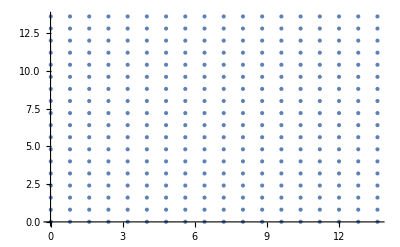

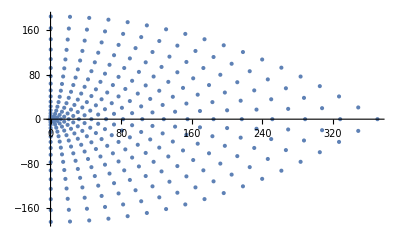

324

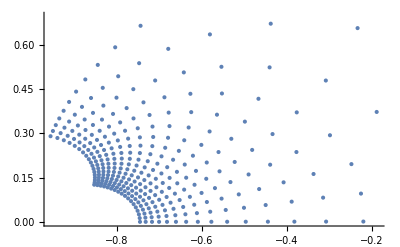

1/324

2/324

3/324

4/324

5/324

6/324

7/324

8/324

9/324

10/324

11/324

12/324

13/324

14/324

15/324

16/324

17/324

18/324

19/324

20/324

21/324

22/324

23/324

24/324

25/324

26/324

27/324

28/324

29/324

30/324

31/324

32/324

33/324

34/324

35/324

36/324

37/324

38/324

39/324

40/324

41/324

42/324

43/324

44/324

45/324

46/324

47/324

48/324

49/324

50/324

51/324

52/324

53/324

54/324

55/324

56/324

57/324

58/324

59/324

60/324

61/324

62/324

63/324

64/324

65/324

66/324

67/324

68/324

69/324

70/324

71/324

72/324

73/324

74/324

75/324

76/324

77/324

78/324

79/324

80/324

81/324

82/324

83/324

84/324

85/324

86/324

87/324

88/324

89/324

90/324

91/324

92/324

93/324

94/324

95/324

96/324

97/324

98/324

99/324

100/324

101/324

102/324

103/324

104/324

105/324

106/324

107/324

108/324

109/324

110/324

111/324

112/324

113/324

114/324

115/324

116/324

117/324

118/324

119/324

120/324

121/324

122/324

123/324

124/324

125/324

126/324

127/324

128/324

129/324

130/324

131/324

132/324

133/324

134/324

135/324

136/324

137/324

138/324

139/324

140/324

141/324

142/324

143/324

144/324

145/324

146/324

147/324

148/324

149/324

150/324

151/324

152/324

153/324

154/324

155/324

156/324

157/324

158/324

159/324

160/324

161/324

162/324

163/324

164/324

165/324

166/324

167/324

168/324

169/324

170/324

171/324

172/324

173/324

174/324

175/324

176/324

177/324

178/324

179/324

180/324

181/324

182/324

183/324

184/324

185/324

186/324

187/324

188/324

189/324

190/324

191/324

192/324

193/324

194/324

195/324

196/324

197/324

198/324

199/324

200/324

201/324

202/324

203/324

204/324

205/324

206/324

207/324

208/324

209/324

210/324

211/324

212/324

213/324

214/324

215/324

216/324

217/324

218/324

219/324

220/324

221/324

222/324

223/324

224/324

225/324

226/324

227/324

228/324

229/324

230/324

231/324

232/324

233/324

234/324

235/324

236/324

237/324

238/324

239/324

240/324

241/324

242/324

243/324

244/324

245/324

246/324

247/324

248/324

249/324

250/324

251/324

252/324

253/324

254/324

255/324

256/324

257/324

258/324

259/324

260/324

261/324

262/324

263/324

264/324

265/324

266/324

267/324

268/324

269/324

270/324

271/324

272/324

273/324

274/324

275/324

276/324

277/324

278/324

279/324

280/324

281/324

282/324

283/324

284/324

285/324

286/324

287/324

288/324

289/324

290/324

291/324

292/324

293/324

294/324

295/324

296/324

297/324

298/324

299/324

300/324

301/324

302/324

303/324

304/324

305/324

306/324

307/324

308/324

309/324

310/324

311/324

312/324

313/324

314/324

315/324

316/324

317/324

318/324

319/324

320/324

321/324

322/324

323/324

324/324

Experiments/Gridcoeff1Grid=324.mat

```mathematica
(*Grid for the second sheet, sqrt(x)+isqrt(y)*)
gridspacing=0.8;
pointsGridsqrt=Flatten[Table[x+I*y,{x,0.01,(2000*MeV),gridspacing},{y,0.01,(2000*MeV),gridspacing}]];
Length[pointsGridsqrt]
ListPlot[Transpose[{Im[pointsGridsqrt],Re[pointsGridsqrt]}]]
pointsGrid=pointsGridsqrt^2;
ListPlot[Transpose[{Im[pointsGrid],Re[pointsGrid]}]]
test3d=Transpose[{Re[pointsGrid],Im[pointsGrid],Abs[pointsGrid]^2}];


Length[pointsGrid]


zGrid=z[pointsGrid];
phiGrid=Arg[zGrid];
ListPlot[Transpose[{Re[zGrid],Im[zGrid]}]]




HsecondsheetS0=Table[1,{z,1,Length[pointsGrid]}];
HsecondsheetP1=Table[1,{z,1,Length[pointsGrid]}];
HsecondsheetD0=Table[1,{z,1,Length[pointsGrid]}];
nmax=30;
mmax=nmax;
vars=Variables[N[(Subscript[f, 0]+Sum[Subscript[ρ, 1][n,m]+Subscript[ρ, 2][n,m],{n,1,nmax},{m,1,mmax}]+Sum[Subscript[σ, 1][n] +Subscript[σ, 2][n] ,{n,1,nmax}]),100]];


Do[
s=pointsGrid[[n]];
HsecondsheetS0[[n]]=Coefficient[hunphy[0, 0, s, nmax, mmax],vars ];
HsecondsheetP1[[n]]=Coefficient[hunphy[1,1, s, nmax, mmax] ,vars ];
HsecondsheetD0[[n]]=Coefficient[hunphy[2, 0, s, nmax, mmax],vars ];

Print[ToString[n]<>"/"<>ToString[Length[pointsGrid]]]
,{n,1,Length[pointsGrid]}]



Export["Experiments/hS0coeffnmaxcomp="<>ToString[nmax]<>"Grid="<>ToString[Length[pointsGrid]]<>".mat",HsecondsheetS0];
Export["Experiments/hP1coeffnmaxcomp="<>ToString[nmax]<>"Grid="<>ToString[Length[pointsGrid]]<>".mat",HsecondsheetP1];
Export["Experiments/hD0coeffnmaxcomp="<>ToString[nmax]<>"Grid="<>ToString[Length[pointsGrid]]<>".mat",HsecondsheetD0];
Export["Experiments/Gridcoeff1"<>"Grid="<>ToString[Length[pointsGrid]]<>".mat",pointsGrid]
```

324

-Graphics-

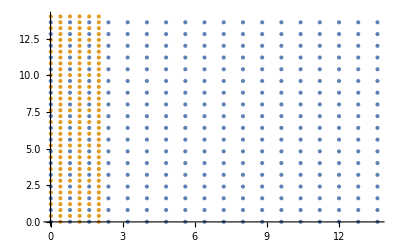

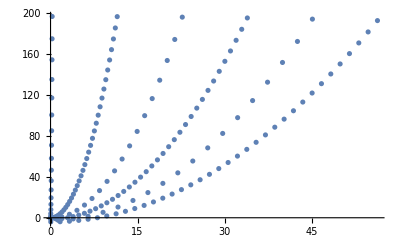

162

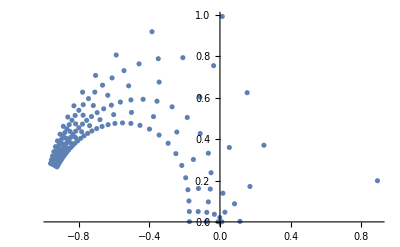

```mathematica
gridspacing=0.8;
pointsGridsqrt=Flatten[Table[x+I*y,{x,0.01,(2000*MeV),gridspacing},{y,0.01,(2000*MeV),gridspacing}]];
Length[pointsGridsqrt]
plotgrid08=ListPlot[Transpose[{Im[pointsGridsqrt],Re[pointsGridsqrt]}]]
pointssave1=Transpose[{Im[pointsGridsqrt],Re[pointsGridsqrt]}];
gridspacing=0.4;
pointsGridsqrt04=Flatten[Table[x+I*y,{x,0.01,(2000*MeV),gridspacing},{y,0.01,(300*MeV),gridspacing}]];
complementpointsGridsqrt=Complement[pointsGridsqrt04,pointsGridsqrt];
pointsGridsqrt=complementpointsGridsqrt;
ListPlot[{pointssave1,Transpose[{Im[pointsGridsqrt],Re[pointsGridsqrt]}]}]


pointsGrid=pointsGridsqrt^2;
ListPlot[Transpose[{Im[pointsGrid],Re[pointsGrid]}]]

Length[pointsGrid]
zGrid=z[pointsGrid];
phiGrid=Arg[zGrid];
ListPlot[Transpose[{Re[zGrid],Im[zGrid]}]]



HsecondsheetS0=Table[1,{z,1,Length[pointsGrid]}];
HsecondsheetP1=Table[1,{z,1,Length[pointsGrid]}];
HsecondsheetD0=Table[1,{z,1,Length[pointsGrid]}];
nmax=30;
mmax=nmax;
vars=Variables[N[(Subscript[f, 0]+Sum[Subscript[ρ, 1][n,m]+Subscript[ρ, 2][n,m],{n,1,nmax},{m,1,mmax}]+Sum[Subscript[σ, 1][n] +Subscript[σ, 2][n] ,{n,1,nmax}]),100]];


Do[
s=pointsGrid[[n]];
HsecondsheetS0[[n]]=Coefficient[hunphy[0, 0, s, nmax, mmax],vars ];
HsecondsheetP1[[n]]=Coefficient[hunphy[1,1, s, nmax, mmax] ,vars ];
HsecondsheetD0[[n]]=Coefficient[hunphy[2, 0, s, nmax, mmax],vars ];

Print[ToString[n]<>"/"<>ToString[Length[pointsGrid]]]
,{n,1,Length[pointsGrid]}]



Export["Experiments/Complement08to04hS0coeffnmaxcomp="<>ToString[nmax]<>"Grid="<>ToString[Length[pointsGrid]]<>".mat",HsecondsheetS0];
Export["Experiments/Complement08to04hP1coeffnmaxcomp="<>ToString[nmax]<>"Grid="<>ToString[Length[pointsGrid]]<>".mat",HsecondsheetP1];
Export["Experiments/Complement08to04hD0coeffnmaxcomp="<>ToString[nmax]<>"Grid="<>ToString[Length[pointsGrid]]<>".mat",HsecondsheetD0];
Export["Experiments/Complement08to04Gridcoeff1"<>"Grid="<>ToString[Length[pointsGrid]]<>".mat",pointsGrid]
```

```mathematica
$KernelCount
```

16

1741

```mathematica
Export["Experiments/Gridcoeff1sqrt"<>"Grid="<>ToString[Length[pointsGrid]]<>".mat",pointsGridsqrt]
```

Experiments/Gridcoeff1sqrtGrid=324.mat

```mathematica
test=Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/Experiments/hS0coeffnmaxcomp=29Grid=324.mat","Data"];
Dimensions[test]
```

{1,324,1741}

```mathematica
Dimensions[HsecondsheetS0]
```

{4,13}

```mathematica
1+2*2*2+2*2
```

13

```mathematica
Export["Experiments/hS0coeffnmaxcomp="<>ToString[nmax]<>"Grid="<>ToString[Length[pointsGrid]]<>".mat",HsecondsheetS0];
Export["Experiments/hP1coeffnmaxcomp="<>ToString[nmax]<>"Grid="<>ToString[Length[pointsGrid]]<>".mat",HsecondsheetP1];
Export["Experiments/hD0coeffnmaxcomp="<>ToString[nmax]<>"Grid="<>ToString[Length[pointsGrid]]<>".mat",HsecondsheetD0];
Export["Experiments/Gridcoeff1"<>"Grid="<>ToString[Length[pointsGrid]]<>".mat",pointsGrid]
Export["Experiments/Gridcoeffcomplement"<>"Grid="<>ToString[Length[pointsGrid]]<>".mat",pointsGrid2]
```

Experiments/Gridcoeff1Grid=4.mat

Experiments/GridcoeffcomplementGrid=4.mat

```mathematica
Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/hP1coeffnmaxcomp=2Grid=4.mat","Data"]
Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/Gridcoeff1Grid=4.mat","Data"]
```

{{{0.+0. ⅈ,0.000189213-0.000456968 ⅈ,0.27397+0.661061 ⅈ,-0.273859-0.66133 ⅈ,2.37364×10^-9-9.84012×10^-10 ⅈ,-0.000189213+0.000456968 ⅈ,-0.0000555846+0.000134306 ⅈ,-0.0000555846+0.000134306 ⅈ,-2.37364×10^-9+9.84012×10^-10 ⅈ,-21.4208-51.6935 ⅈ,-12.5958-30.3815 ⅈ,21.4208+51.6935 ⅈ,12.5958+30.3815 ⅈ},{0.+0. ⅈ,-0.139095-0.00650366 ⅈ,0.0711411-0.0429531 ⅈ,0.0317788+0.0731021 ⅈ,-0.0391551-0.0115476 ⅈ,0.139095+0.00650366 ⅈ,-0.05146-0.0150745 ⅈ,-0.05146-0.0150745 ⅈ,0.0391551+0.0115476 ⅈ,0.217414+0.190726 ⅈ,0.0110433-0.175757 ⅈ,-0.217414-0.190726 ⅈ,-0.0110433+0.175757 ⅈ},{0.+0. ⅈ,-0.0713132+0.1227 ⅈ,-0.0733273-0.123311 ⅈ,0.030507-0.0471937 ⅈ,0.0270198+0.0474292 ⅈ,0.0713132-0.1227 ⅈ,0.0214102+0.0852525 ⅈ,0.0214102+0.0852525 ⅈ,-0.0270198-0.0474292 ⅈ,0.141919+6.43766×10^-7 ⅈ,-0.0545861-5.06806×10^-7 ⅈ,-0.141919-6.43766×10^-7 ⅈ,0.0545861+5.06806×10^-7 ⅈ},{0.+0. ⅈ,-0.131577+0.062146 ⅈ,0.0333679-0.106488 ⅈ,0.0802071+0.0102046 ⅈ,-0.0397356+0.0389728 ⅈ,0.131577-0.062146 ⅈ,-0.0567875+0.0481419 ⅈ,-0.0567875+0.0481419 ⅈ,0.0397356-0.0389728 ⅈ,0.193668+0.068976 ⅈ,-0.0781062-0.0790018 ⅈ,-0.193668-0.068976 ⅈ,0.0781062+0.0790018 ⅈ}}}

{{0.0001+0.0001 ⅈ,0.0001+16.0801 ⅈ,16.0801+0.0001 ⅈ,16.0801+16.0801 ⅈ}}

### Rescale the amplitudes:

```mathematica
H=Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/hmatyifeiM=81nmax=29lmax=15.mat","Data"];
Dimensions[H[[1]]];
```

{3,7,81,1741}

```mathematica
reScale[vnu_,l_]:=N[((Sqrt[vnu]-2)/(Sqrt[vnu]+1))^(l/2),30];
```

```mathematica
vnu=Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/vnuvalsM=81nmax=29lmax=15.mat","Data"];
(*Export["/Users/rafaelcordoba/Documents/MATLAB/Experiments/test23.mat",vnu[[1]]]*)

Dimensions[vnu2];
```

/Users/rafaelcordoba/Documents/MATLAB/Experiments/test23.mat

{{4.00038,4.00339,4.00942,4.01848,4.03062,4.04585,4.06424,4.08582,4.11068,4.13889,4.17054,4.20573,4.24457,4.28719,4.33373,4.38434,4.43921,4.49851,4.56247,4.63131,4.70528,4.78467,4.86977,4.96093,5.05851,5.16293,5.27461,5.39406,5.52181,5.65847,5.80467,5.96116,6.12874,6.30829,6.50081,6.7074,6.92929,7.16786,7.42465,7.70138,8.,8.32272,8.67202,9.05073,9.46207,9.90973,10.3979,10.9315,11.5162,12.1584,12.8659,13.6475,14.5138,15.4773,16.5528,17.7584,19.1155,20.6505,22.3956,24.3908,26.686,29.3442,32.4459,36.0954,40.4292,45.6295,51.9435,59.7128,69.4214,81.7724,97.8188,119.196,148.556,190.429,253.084,352.949,526.584,869.603,1703.14,4728.57,42546.5}}

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{1,81}

```mathematica
ImH=Im[H]; ReH=Re[H];ImH2=Im[H];
```

{1,3,7,81,1741}

```mathematica
Export["Experiments/hS0coeffnmaxcomp="<>ToString[nmax]<>".mat",HsecondsheetS0];
Export["Experiments/hP1coeffnmaxcomp="<>ToString[nmax]<>".mat",HsecondsheetP1];
Export["Experiments/hD0coeffnmaxcomp="<>ToString[nmax]<>".mat",HsecondsheetD0];

Dimensions[HsecondsheetD0]
Dimensions[HsecondsheetS0]
Dimensions[HsecondsheetP1]
```

{324}

{324}

{324}

```mathematica
pointsGridsqrt=Flatten[Table[x+I*y,{x,0.01,(1000*MeV),0.4},{y,0.01,(1000*MeV),0.4}]];

pointsGridsqrt2=Flatten[Table[x+I*y,{x,0.01,(2000*MeV),0.4},{y,0.01,(2000*MeV),0.4}]];
pointsGridsqrt2=Complement[pointsGridsqrt2,pointsGridsqrt];
```

$Aborted

### Rescale the amplitudes:

```mathematica
reScale[vnu_,l_]:=N[((Sqrt[vnu]-2)/(Sqrt[vnu]+1))^(l/2),100];
ll[l_,i_]:=0;
ll[l_,i_]:=2*(l-1)+1 /; Mod[i,2]==0;
ll[l_,i_]:=2*(l-1)/; Mod[i,2]==1;
Do[
M=49;
H=Import["hmatyifeiM=49nmax="<>ToString[nmax]<>"lmax=15.mat"][[1]];
vnu=Import["vnuvalsM=49nmax="<>ToString[nmax]<>"lmax=15.mat"][[1]];
Print[Dimensions[H]];
Print[Dimensions[vnu]];


reH=Table[1,{i,1,Dimensions[H][[1]]},{l,1,Dimensions[H][[2]]},{iternu,1,Dimensions[H][[3]]},{k,1,Dimensions[H][[4]]}];
imH =Table[1,{i,1,Dimensions[H][[1]]},{l,1,Dimensions[H][[2]]},{iternu,1,Dimensions[H][[3]]},{k,1,Dimensions[H][[4]]}];
imH2=Table[1,{i,1,Dimensions[H][[1]]},{l,1,Dimensions[H][[2]]},{iternu,1,Dimensions[H][[3]]},{k,1,Dimensions[H][[4]]}];
Do[
s=vnu[[iternu]];
reH[[i,l,iternu,All]]=Re[H[[i,l,iternu,All]]]/reScale[s,ll[l,i]];
imH[[i,l,iternu,All]]=Im[H[[i,l,iternu,All]]]/reScale[s,ll[l,i]];
imH2[[i,l,iternu,All]]=Im[H[[i,l,iternu,All]]]/(reScale[s,ll[l,i]])^2;

,{i,1,Dimensions[H][[1]]},{l,1,Dimensions[H][[2]]},{iternu,1,Dimensions[H][[3]]}];
Export["rescaleReHM=49nmax="<>ToString[nmax]<>"lmax=15.mat",reH];
Export["rescaleImHM=49nmax="<>ToString[nmax]<>"lmax=15.mat",imH];
Export["rescaleImH2M=49nmax="<>ToString[nmax]<>"lmax=15.mat",imH2];


,{nmax,20,50}]
```

{3,16,49,5101}

{49}

```mathematica
Dimensions[reH]
```

{3,16,49,5101}

#### Veczz and Vecsin

```mathematica
Do[
M=49;
vphi=Table[N[(i-1/2)Pi/M,100],{i,1,M}];
vnu=N[nuphi[vphi],100];

veczz=Table[i*j,{i,1,Length[vnu]},{j,1,nmaxtilde}];
vecsin=Table[i*j,{i,1,Length[vnu]},{j,1,nmaxtilde}];

Do[
veczz[[i,j]]=Exp[I*vphi[[i]]*j];
vecsin[[i,j]]=Sin[vphi[[i]]*j];
,{i,1,Length[vnu]},{j,1,nmaxtilde}];
Export["veczzM="<>ToString[M]<>"nmaxtilde="<>ToString[nmaxtilde]<>".mat",veczz];
Export["vecsinM="<>ToString[M]<>"nmaxtilde="<>ToString[nmaxtilde]<>".mat",vecsin];
,{nmaxtilde,1,M}]
```

```mathematica
Dimensions[veczz]
Dimensions[vecsin]
```

{49,49}

{49,49}

{81,10}

```mathematica
Do[
M=49;
vphi=Table[N[(i-1/2)Pi/M,100],{i,1,M}];
vnu=N[nuphi[vphi],100];


Export["vnuvalsM=49nmax="<>ToString[nmax]<>"lmax=15.mat",vnu];
,{nmax,10,50}]
```

```mathematica
vnu
```

{4.001027831640246854229781425887409746110610596469462732466737646934063259147013308540112101305207239,4.009263176146956975568437225569205175393596963662044943348742949988948769302452627048121588557675592,4.025801799699522458949158081363548477733537637215133791179401235725209383269637669404724861942125832,4.050780765542936146405183099043258138347859807734120431621368950631924350226298052216016453489495422,4.084408690119173072628842496122825519942922902222828769902961385350133060878726796898892729592465312,4.126969471878577930245999523902671435329268507279744928549808745852680727719233174963922488417780989,4.178827439717483710492133546003193813177785420498246548167014800560740977410977746147521953607757058,4.240434083154654691852818619858196741832939041128073518279822041671847427199625478821886673559087772,4.312336581061791595390139179127180814882600296590311032515321442584169295026021047742867881520589486,4.395188411314101062677823109844740630607089132226672861291303983221794364379980457891514452275489143,4.489762403860511294397928276709596555412368426695366851587791789208155623686592601136501656825512471,4.596966699254186442408998808778114071680612202902808419070807899118871492515478580768101929088957152,4.717864199966457830005411623096873932927454355207700158943308596446257413125758680406086376890723091,4.853696261255157290120237049821990461620627069320968846075288181443754399651681486047362352868004687,5.005911573300888224882285547066311575412549492938230248998328088098216896460826389749710621128581356,5.176201452153527067966931264573097455106437157290303731335973348177966164572544366487561083873262484,5.366543104859656983061501584302282103020359178101808842048613979913787402766707386615119123603460225,5.579252893211109576726366200533096966592137595105075060057899889441299446566613562750647173049532986,5.817052231760396930105513904502977562571428136769702530256628693984062050491175493087498178235925845,6.083149576863424192292717840714524558001129001009977646141439395538296853822015095637609300011739132,6.38134307701575349090242404185192487269616418800317974613778244354965986362308183022329217195528102,6.71614997972333742528151361723407946160018287155478069022135987522926847689681163650747773847784001,7.09297100054038483822579067875693957567524140334189439623612845288056686397118099774244598063704541,7.51830081302811579814882856479241512375751576527647163398745375327915078722154718212221268723689402,8.,8.5476498032097459530335488791426930468892257424355099486007542734976533337782312143575902502668364,9.17301972673024692822275139620477861735720385673594090380423711596052428248275163064589275312033038,9.89069091156362938193272422851589799611832786204976377152032963398358030018515855910903501913190326,10.7188974803457745998977924768359230637967473470466815070536130304121857708938512647066332330913797,11.6806774596047140823170135061315440071157777986580926299953005886212602024662645119372000960626595,12.8054705970113344473795781203014254380317724733640666654933308198297103669583592219390937940927767,14.131372922462754767093480391334478060783184048293701173217433871291515339348957169982337155314201,15.7083756400374862385128225869906383088987123415079558057612307036162560316771031576152903882235878,17.6031119250068347228393852503699090293964595034970006847557422587680713492207992207382638030846219,19.905970688354015700892522370945218742211336862940797875122556784370297148712593709938138956620089,22.7420288996882870201540786373647995563996815841576692683160875597663745553337879518133562842177923,26.2883381017574065199323328047119120908307388266487644064789049382956286229643535321136831968098846,30.8021650453692275693568861730199176594695393677872815724116846298376374598232353832726267574940626,36.6689020510380842963605030819271661070434916222886722214905560761344122611911486562356068730382368,44.4870171845271669104809123798243848114427203830737567894555655832937254386649888635656580782500712,55.2267885676657740186077952725296974253660935661483117590918383098180431748962046791087286895784777,70.546305707033647126207336367362235098224734344527006177188895943334005982859220061638894672124863,93.471727746464527696583814757629880837761533866619787866143886056758486551890853488793058221335337,130.01454320689737652281014527066503460193948921037058160128239676218662555379706096005499059636698,193.55394257878275606427824597240930341421651454305559348698862079124471546381066163813142344218289,319.07992896388460391901653895045240417182095849988306426202494942329269297898038995767889068828302,624.11178236904648291614982234011591017312881072060044431404299654399521787362713285824648541733743,1731.2693238437577107227382857368480017410156519537772457583599024966667870856426810866059441283919,15570.75176506269205999223491773891039123130887652598740119297789823619376752086222957281396994743}

```mathematica
vnu
```

{4.001027831640246854229781425887409746110610596469462732466737646934063259147013308540112101305207239,4.009263176146956975568437225569205175393596963662044943348742949988948769302452627048121588557675592,4.025801799699522458949158081363548477733537637215133791179401235725209383269637669404724861942125832,4.050780765542936146405183099043258138347859807734120431621368950631924350226298052216016453489495422,4.084408690119173072628842496122825519942922902222828769902961385350133060878726796898892729592465312,4.126969471878577930245999523902671435329268507279744928549808745852680727719233174963922488417780989,4.178827439717483710492133546003193813177785420498246548167014800560740977410977746147521953607757058,4.240434083154654691852818619858196741832939041128073518279822041671847427199625478821886673559087772,4.312336581061791595390139179127180814882600296590311032515321442584169295026021047742867881520589486,4.395188411314101062677823109844740630607089132226672861291303983221794364379980457891514452275489143,4.489762403860511294397928276709596555412368426695366851587791789208155623686592601136501656825512471,4.596966699254186442408998808778114071680612202902808419070807899118871492515478580768101929088957152,4.717864199966457830005411623096873932927454355207700158943308596446257413125758680406086376890723091,4.853696261255157290120237049821990461620627069320968846075288181443754399651681486047362352868004687,5.005911573300888224882285547066311575412549492938230248998328088098216896460826389749710621128581356,5.176201452153527067966931264573097455106437157290303731335973348177966164572544366487561083873262484,5.366543104859656983061501584302282103020359178101808842048613979913787402766707386615119123603460225,5.579252893211109576726366200533096966592137595105075060057899889441299446566613562750647173049532986,5.817052231760396930105513904502977562571428136769702530256628693984062050491175493087498178235925845,6.083149576863424192292717840714524558001129001009977646141439395538296853822015095637609300011739132,6.38134307701575349090242404185192487269616418800317974613778244354965986362308183022329217195528102,6.71614997972333742528151361723407946160018287155478069022135987522926847689681163650747773847784001,7.09297100054038483822579067875693957567524140334189439623612845288056686397118099774244598063704541,7.51830081302811579814882856479241512375751576527647163398745375327915078722154718212221268723689402,8.,8.5476498032097459530335488791426930468892257424355099486007542734976533337782312143575902502668364,9.17301972673024692822275139620477861735720385673594090380423711596052428248275163064589275312033038,9.89069091156362938193272422851589799611832786204976377152032963398358030018515855910903501913190326,10.7188974803457745998977924768359230637967473470466815070536130304121857708938512647066332330913797,11.6806774596047140823170135061315440071157777986580926299953005886212602024662645119372000960626595,12.8054705970113344473795781203014254380317724733640666654933308198297103669583592219390937940927767,14.131372922462754767093480391334478060783184048293701173217433871291515339348957169982337155314201,15.7083756400374862385128225869906383088987123415079558057612307036162560316771031576152903882235878,17.6031119250068347228393852503699090293964595034970006847557422587680713492207992207382638030846219,19.905970688354015700892522370945218742211336862940797875122556784370297148712593709938138956620089,22.7420288996882870201540786373647995563996815841576692683160875597663745553337879518133562842177923,26.2883381017574065199323328047119120908307388266487644064789049382956286229643535321136831968098846,30.8021650453692275693568861730199176594695393677872815724116846298376374598232353832726267574940626,36.6689020510380842963605030819271661070434916222886722214905560761344122611911486562356068730382368,44.4870171845271669104809123798243848114427203830737567894555655832937254386649888635656580782500712,55.2267885676657740186077952725296974253660935661483117590918383098180431748962046791087286895784777,70.546305707033647126207336367362235098224734344527006177188895943334005982859220061638894672124863,93.471727746464527696583814757629880837761533866619787866143886056758486551890853488793058221335337,130.01454320689737652281014527066503460193948921037058160128239676218662555379706096005499059636698,193.55394257878275606427824597240930341421651454305559348698862079124471546381066163813142344218289,319.07992896388460391901653895045240417182095849988306426202494942329269297898038995767889068828302,624.11178236904648291614982234011591017312881072060044431404299654399521787362713285824648541733743,1731.2693238437577107227382857368480017410156519537772457583599024966667870856426810866059441283919,15570.75176506269205999223491773891039123130887652598740119297789823619376752086222957281396994743}

```mathematica
test1=Import["/Users/rafaelcordoba/Documents/MATLAB/Experiments/Experiments/hP1coeffnmaxcomp=50Grid=64.mat","Data"][[1]];
```

-1.2734×10^-53-2.51136×10^-53 ⅈ